# 2.3 Damped pendulum

#### Consider the dynamical system for the pendulum in dimensionless variables (x,y,t’) with Here, σ is a dimensionless parameter. a) For arbitrary , calculate and classify the fixed points as a function of . Due to periodicity, you can limit your investigation to . Make a table listing the different cases. See on the end of this PDF. b) For each case, make a phase portrait (plot a set of representative trajectories) centered around the investigated fixed point, and upload it as a .png or .pdf. Use for example NDSolve in Mathematica with a set of suitably chosen initial conditions (you may use StreamPlot to get an idea of what you are looking at, but it is not accurate enough to be an acceptable solution). Plot Phase portraits. This time must be numerical! NDSolve[ ], (StreamPlot is not accepted!) Plot the fix points

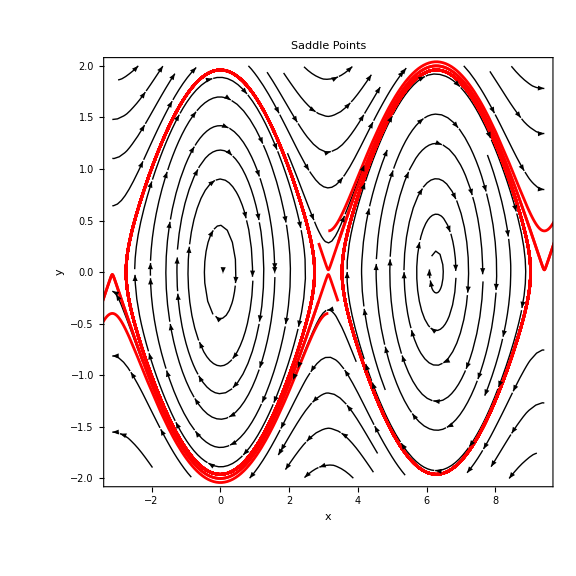

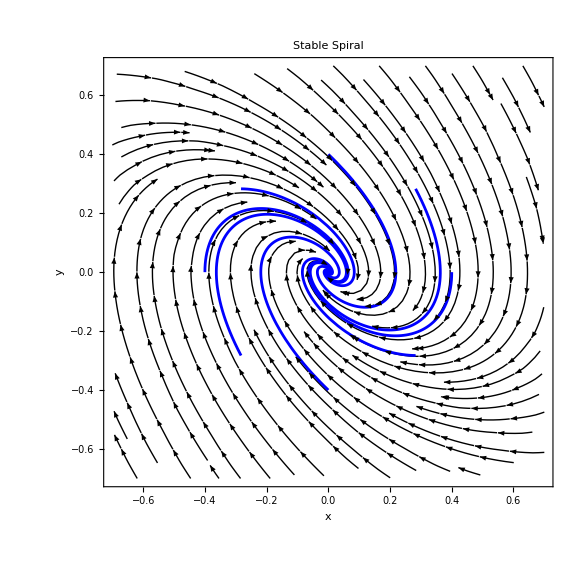

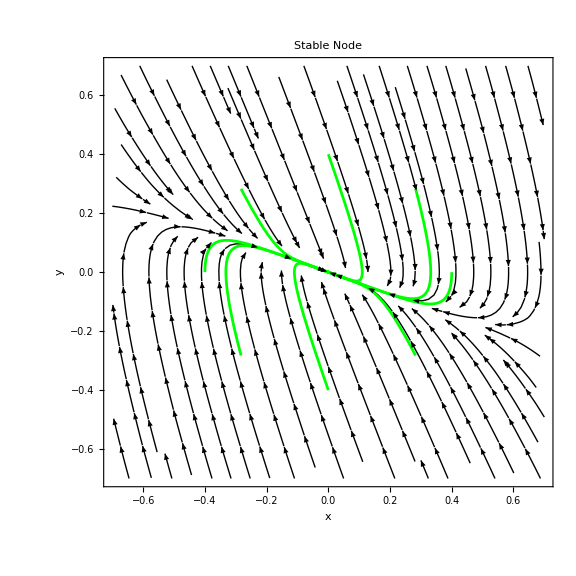

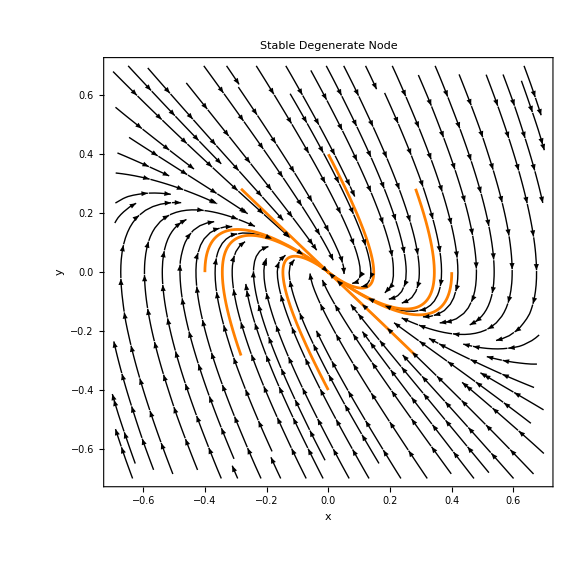

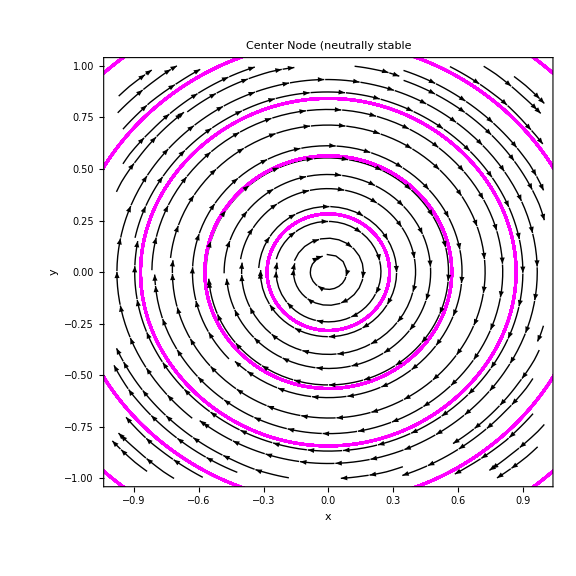

```mathematica
ClearAll["Global`*"]

(*As seen in a) for different values for sigma different fix points appear*)
SaddlePoint= 0; 
StableSpiral = 1; 
StableNode = 3; 
StableDegenerateNode = 2; 
CenterNode = 0; 

Equation1 = x'[t] == y[t];
Equation2 = y'[t] == -Sin[x[t]] - SaddlePoint*y[t];
Equation21 = y'[t] == -Sin[x[t]] - StableSpiral*y[t];
Equation22 = y'[t] == -Sin[x[t]] - StableNode*y[t];
Equation23 = y'[t] == -Sin[x[t]] - StableDegenerateNode*y[t];
Equation24 = y'[t] == -Sin[x[t]] - CenterNode*y[t];

FixPoint1 = {Pi, 0};
FixPoint2 = {0, 0};
FixPoint3 = {0, 0};

Radius1 = 0.4;
Radius2 = 0.2;

System1 = {Equation1, Equation2};
System21 = {Equation1, Equation21};
System22 = {Equation1, Equation22};
System23 = {Equation1, Equation23};
System24 = {Equation1, Equation24};

numTrajectories = 8;

StartingPoint1 = Table[{x[0] == FixPoint1[[1]] + Radius1 Cos[2 Pi i/numTrajectories], 
    y[0] == FixPoint1[[2]] + Radius1 Sin[2 Pi i/numTrajectories]}, {i, 0, numTrajectories - 1}];
StartingPoint2 = Table[{x[0] == FixPoint2[[1]] + Radius1 Cos[2 Pi i/numTrajectories], 
    y[0] == FixPoint2[[2]] + Radius1 Sin[2 Pi i/numTrajectories]}, {i, 0, numTrajectories - 1}];
StartingPoint3 = Table[{x[0] == FixPoint3[[1]] + Radius2 *i, 
    y[0] == FixPoint2[[2]] + Radius2 * i}, {i, 0, numTrajectories - 1}];

t0 = 0;
tMax = 120;

Solution1 = Table[NDSolve[{System1, StartingPoint}, {x, y}, {t, t0, tMax}], {StartingPoint, StartingPoint1}];
Solution21 = Table[NDSolve[{System21, startingPoint}, {x, y}, {t, t0, tMax}], {startingPoint, StartingPoint2}];
Solution22 = Table[NDSolve[{System22, startingPoint}, {x, y}, {t, t0, tMax}], {startingPoint, StartingPoint2}];
Solution23 = Table[NDSolve[{System23, startingPoint}, {x, y}, {t, t0, tMax}], {startingPoint, StartingPoint2}];
Solution24 = Table[NDSolve[{System24, startingPoint}, {x, y}, {t, t0, tMax}], {startingPoint, StartingPoint3}];

StreamPlot10 = StreamPlot[{y, -Sin[x] - SaddlePoint*y}, {x, -Pi, 3*Pi}, {y, -2, 2}, 
   PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black), 
   StreamStyle -> Directive[Black], StreamColorFunction->None];
StreamPlot21 = StreamPlot[{y, -Sin[x] - StableSpiral*y}, {x, -0.7, 0.7}, {y, -0.7, 0.7}, 
   PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black), 
   StreamStyle -> Directive[Black], StreamColorFunction->None];
StreamPlot22 = StreamPlot[{y, -Sin[x] - StableNode*y}, {x, -0.7, 0.7}, {y, -0.7, 0.7}, 
   PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black), 
   StreamStyle -> Directive[Black], StreamColorFunction->None];
StreamPlot23 = StreamPlot[{y, -Sin[x] - StableDegenerateNode*y}, {x, -0.7, 0.7}, {y, -0.7, 0.7}, 
   PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black), 
   StreamStyle -> Directive[Black], StreamColorFunction->None];
StreamPlot24 = StreamPlot[{y, -Sin[x] - CenterNode*y}, {x, -1, 1}, {y, -1, 1}, 
   PlotRange -> All, ImageSize -> Large, ColorFunction -> (Black), 
   StreamStyle -> Directive[Black], StreamColorFunction->None];

(* Plot trajectories for the different Systems *)
TrajectoryPlot10 = ParametricPlot[Evaluate[{x[t], y[t]} /. #] & /@ Solution1, {t, t0, tMax}, PlotStyle -> Red];
TrajectoryPlot21 = ParametricPlot[Evaluate[{x[t], y[t]} /. #] & /@ Solution21, {t, t0, tMax}, PlotStyle -> Blue];
TrajectoryPlot22 = ParametricPlot[Evaluate[{x[t], y[t]} /. #] & /@ Solution22, {t, t0, tMax}, PlotStyle -> Green];
TrajectoryPlot23 = ParametricPlot[Evaluate[{x[t], y[t]} /. #] & /@ Solution23, {t, t0, tMax}, PlotStyle -> Orange];
TrajectoryPlot24 = ParametricPlot[Evaluate[{x[t], y[t]} /. #] & /@ Solution24, {t, t0, tMax}, PlotStyle -> Magenta];

(* Label the plot *)
Show[StreamPlot10, TrajectoryPlot10, FrameLabel -> {"x", "y"}, PlotLabel -> "Saddle Points"]
Show[StreamPlot21, TrajectoryPlot21, FrameLabel -> {"x", "y"}, PlotLabel -> "Stable Spiral"]
Show[StreamPlot22, TrajectoryPlot22, FrameLabel -> {"x", "y"}, PlotLabel -> "Stable Node"]
Show[StreamPlot23, TrajectoryPlot23, FrameLabel -> {"x", "y"}, PlotLabel -> "Stable Degenerate Node"]
Show[StreamPlot24, TrajectoryPlot24, FrameLabel -> {"x", "y"}, PlotLabel -> "Center Node (neutrally stable"]
```